```mathematica
ClearAll[data27]
data27=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\27\\27apr_"<>ToString[i]<>"ac.dat"],{i,1,7}];
```

```mathematica
amplitude=Table[data27[[i]][[All,2]]*data27[[6]][[1,2]]/data27[[i]][[1,2]],{i,1,7}];
```

```mathematica
nonLogorifmicTime = 
  Table[Transpose[{data27[[i]][[All, 3]]-1.68, amplitude[[i]]}], {i, 
    1, 7}];
```

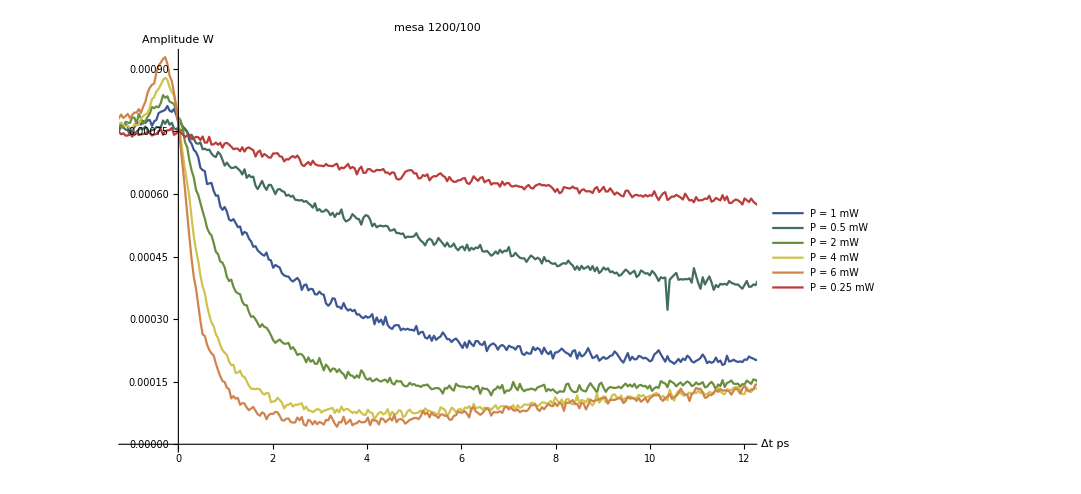

```mathematica
ListLinePlot[Table[nonLogorifmicTime[[i]],{i,1,6}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW","P = 0.25 mW"},ImageSize->800,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{-1,12},All},PlotStyle->"DarkRainbow"]
```

```mathematica
sample=MeanFilter[nonLogorifmicTime[[4]],{4,0}];
```

```mathematica
sample2=MeanFilter[nonLogorifmicTime[[1]],{4,0}];
```

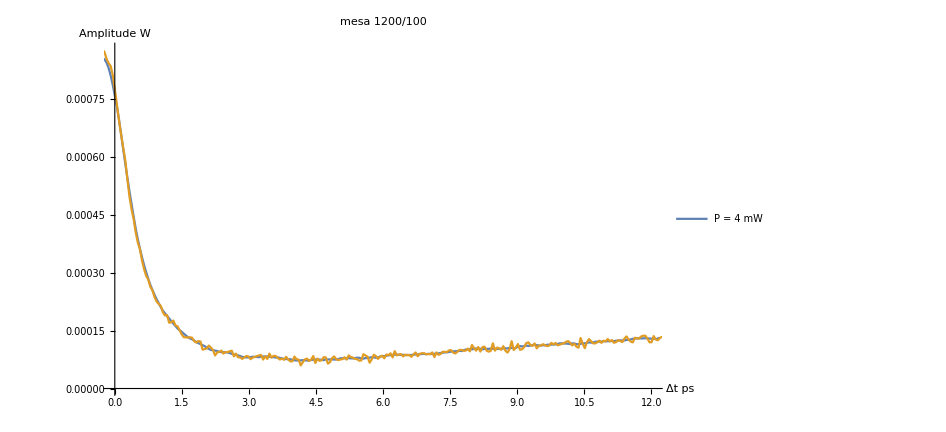

```mathematica
ListLinePlot[{sample,nonLogorifmicTime[[4]]},PlotLegends->{"P = 4 mW"},ImageSize->700,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,12},All}]
```

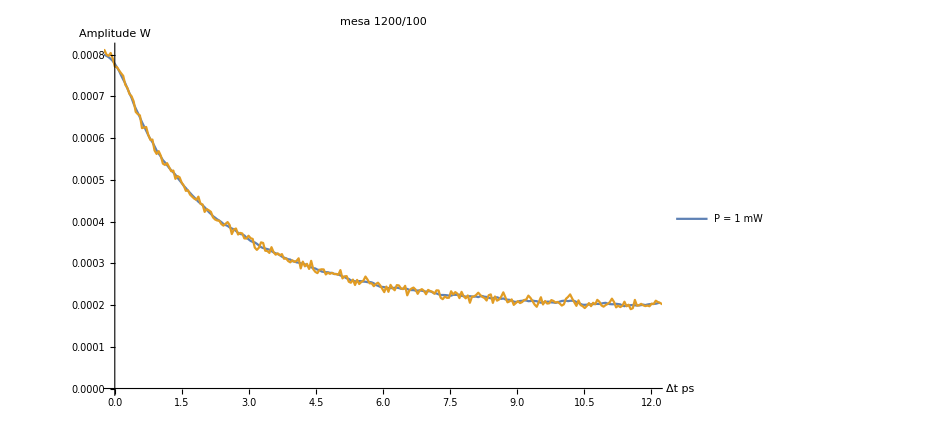

```mathematica
ListLinePlot[{sample2,nonLogorifmicTime[[1]]},PlotLegends->{"P = 1 mW"},ImageSize->700,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,12},All}]
```

```mathematica
len=sample2//Length
```

300

```mathematica
forFit=Table[sample[[i]],{i,37,270,15}];
```

```mathematica
forFit2 =Table[sample2[[i]],{i,37,270,15}];
```

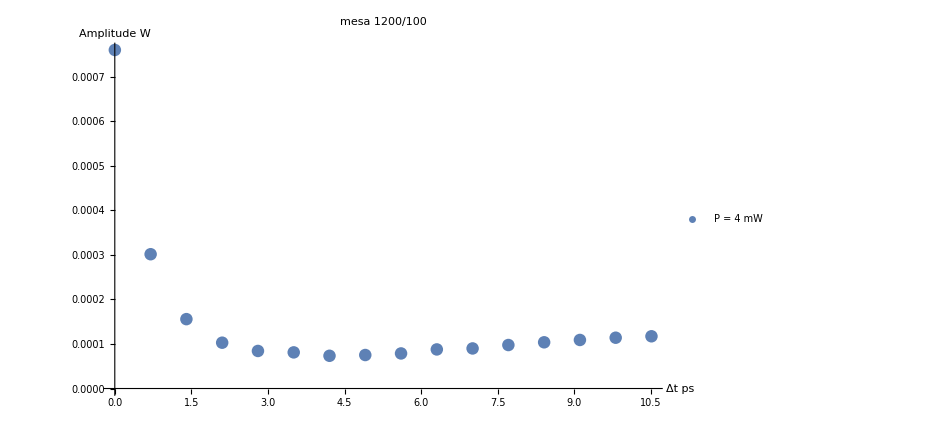

```mathematica
ListPlot[forFit,PlotLegends->{"P = 4 mW"},ImageSize->700,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->All]
```

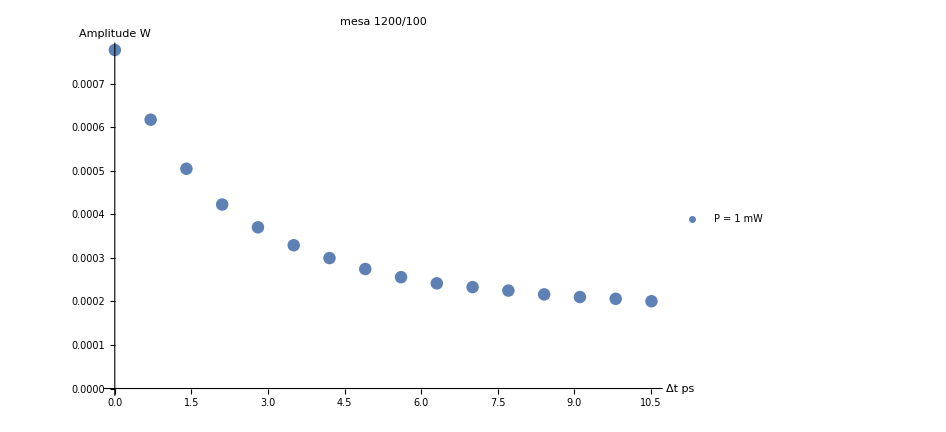

```mathematica
ListPlot[forFit2,PlotLegends->{"P = 1 mW"},ImageSize->700,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->All]
```

```mathematica
steps=forFit[[;;,1]]
```

{0.00117567,0.701666,1.40216,2.10265,2.80314,3.50363,4.20412,4.9046,5.60509,6.30558,7.00607,7.70656,8.40705,9.10754,9.80803,10.5085}

#### Плазменная частота для накачки 4 мВт

```mathematica
3.3*8^(1/2)
```

9.33381

```mathematica
w=9.333809511662427;
```

```mathematica
Manipulate[
solIn=NDSolve[{p''[x]+a*p'[x]+a*r*p[x]+w^2/n*p[x]*Exp[-x*c]==10^3*w^2*e*Exp[-x*c], p[0]==0, p'[0]==0},  p[x],{x,0, 10}];
Show[ListPlot[forFit],Plot[(1-p[x]/n/e/10^3)/forFit[[1,2]]^-1 /. solIn, {x,0,11},PlotRange->All],PlotRange->All],
{{a,14.76}, 10,15}, {{c,0.762},0.1,1.2}, {{n,3.23},0.1,3.5},{{e,3.22},1,20}, {{r,0.010473}, 1/100000, 0.015}]
```

```mathematica
(*{{a,11}, 1,100}, {{c,1.2},0.001,1.5}, {{n,3},1,1000}, {{e,3.5},2,5}, {{w,8},0.1,100}, {{r,1/1000}, 1/100000, 1/100}*)
```

```mathematica
w2=3.3*2^(1/2)
```

4.6669

```mathematica
(*14.,0.762,3.38,3,0.010623*)
```

```mathematica
Manipulate[
solIn=NDSolve[{p''[x]+a*p'[x]+a*r*p[x]+w2^2/n*p[x]*Exp[-x*c]==10^3*w2^2*e*Exp[-x*c], p[0]==0, p'[0]==0},  p[x],{x,0, 10}];
Show[ListPlot[forFit2],Plot[(1-p[x]/n/e/10^3)/forFit2[[1,2]]^-1 /. solIn, {x,0,11},PlotRange->All],PlotRange->All],
{{a,14.}, 10,20}, {{c,0.762},0.1,1.2}, {{n,3.38},0.1,3.5},{{e,3.22},1,20}, {{r,0.010623}, 0, 0.015}]
```

```mathematica
sol=
Table[{
{a,c,n,e,r},
-NDSolveValue[{p''[x]+a*p'[x]+a*r*p[x]+w^2/n*p[x]*Exp[-x*c]==10^3*w^2*e*Exp[-x*c], p[0]==0, p'[0]==0},  p,{x,0,11}]/@steps/n/e/10^3/forFit[[1,2]]^(-1)
},
{a,13.76,15.76,.5}, {c,0.742,0.782,0.01}, {n,3.13,3.43,.05}, {e,3,3}, {r,0.009473,0.011473,.0005}
];
```

```mathematica
Dimensions[sol]
```

{5,5,7,1,5,2}

```mathematica
Dimensions[sol][[1;;5]]/.List->Times
```

875

```mathematica
Manipulate[ListPlot[{forFit,Transpose[{steps,forFit[[1,2]]+sol[[a,c,n,1,r]][[2]]}]},PlotRange->All]
,{a, 1,5,1}, {c,1,5,1}, {n,1,7,1}, {r, 1,5,1}]
```

```mathematica
table=Flatten[Table[{{a,c,n,1,r},Total[((forFit[[1,2]]+sol[[a,c,n,1,r]][[2]])-forFit[[All,2]])^2]},
{a, 1,5,1}, {c,1,5,1}, {n,1,7,1}, {r, 1,5,1}],3];
```

```mathematica
Dimensions[table]
```

{875,2}

```mathematica
Min[table[[All,2]]]
```

6.21515×10^-10

```mathematica
Position[table[[All,2]],Min[table[[All,2]]]]
```

{{207}}

```mathematica
table[[207]][[1]]
```

{2,1,7,1,2}

```mathematica
sol[[2,1,7,1,2]]
```

{{14.26,0.742,3.43,3,0.009973},{-1.32663×10^-8,-0.000476462,-0.00061052,-0.000653872,-0.000670693,-0.00067712,-0.000678662,-0.000677632,-0.000675153,-0.000671828,-0.000668,-0.000663876,-0.00065958,-0.000655189,-0.000650752,-0.000646297}}

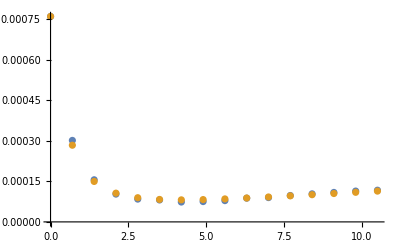

```mathematica
ListPlot[{forFit,Transpose[{steps,forFit[[1,2]]+sol[[2,1,7,1,2]][[2]]}]},PlotRange->All]
```

```mathematica
(*{14.26,0.742,3.4299999999999997,3,0.009973000000000001}*)
```

```mathematica
step2=
Table[{
{a,c,n,e,r},
-NDSolveValue[{p''[x]+a*p'[x]+a*r*p[x]+w^2/n*p[x]*Exp[-x*c]==10^3*w^2*e*Exp[-x*c], p[0]==0, p'[0]==0},  p,{x,0,11}]/@steps/n/e/10^3/forFit[[1,2]]^(-1)
},
{a, 14,14.5,.1}, {c,0.722,0.762,0.01}, {n,3.33,3.53,.05}, {e,3,3}, {r,0.009873,0.010973,.00025}
];
```

```mathematica
Dimensions[step2]
```

{6,5,5,1,5,2}

```mathematica
table2=Flatten[Table[{{a,c,n,1,r},Total[((forFit[[1,2]]+step2[[a,c,n,1,r]][[2]])-forFit[[All,2]])^2]},
{a, 1,6,1}, {c,1,5,1}, {n,1,5,1}, {r, 1,5,1}],3];
```

```mathematica
Dimensions[table2]
```

{750,2}

```mathematica
Min[table2[[All,2]]]
```

4.6422×10^-10

```mathematica
Position[table2[[All,2]],Min[table2[[All,2]]]]
```

{{149}}

```mathematica
table[[149]][[1]]
```

{1,5,2,1,4}

```mathematica
step2[[1,5,2,1,4]]
```

{{14.,0.762,3.38,3,0.010623},{-1.34638×10^-8,-0.000484955,-0.000616463,-0.000657743,-0.00067326,-0.000678793,-0.000679661,-0.000678084,-0.000675137,-0.000671399,-0.000667196,-0.000662724,-0.000658102,-0.000653399,-0.000648662,-0.000643917}}

```mathematica
1000/14//N
```

71.4286

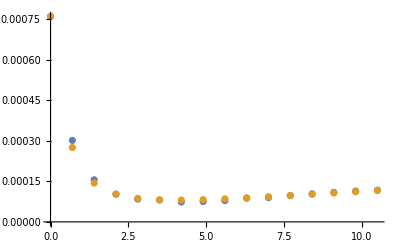

```mathematica
ListPlot[{forFit,Transpose[{steps,forFit[[1,2]]+step2[[1,5,2,1,4]][[2]]}]},PlotRange->All]
```

#### Случайный (с нормальным распределением) набор параметров.

```mathematica
param[m_,d_]:=RandomVariate[NormalDistribution[m,d],7]
```

```mathematica
7^4
```

2401

```mathematica
step3=
Table[{
{a,c,n,e,r},
-NDSolveValue[{p''[x]+a*p'[x]+a*r*p[x]+w^2/n*p[x]*Exp[-x*c]==10^3*w^2*e*Exp[-x*c], p[0]==0, p'[0]==0},  p,{x,0,11}]/@steps/n/e/10^3/forFit[[1,2]]^(-1)
},
{a, param[14,.3]}, {c,param[0.762,.01]}, {n,param[3.38,.2]}, {e,3,3}, {r,param[0.010623,.0008]}
];
```

```mathematica
RandomVariate[NormalDistribution[0.010623,.0008],6]
```

{0.0110628,0.010697,0.00889089,0.0124399,0.0110771,0.00965074}

```mathematica
Dimensions[step3]
```

{7,7,7,1,7,2}

```mathematica
table3=Flatten[Table[{{a,c,n,1,r},Total[((forFit[[1,2]]+step3[[a,c,n,1,r]][[2]])-forFit[[All,2]])^2]},
{a, 1,7,1}, {c,1,7,1}, {n,1,7,1}, {r, 1,7,1}],3];
```

```mathematica
Dimensions[table3]
```

{2401,2}

```mathematica
Min[table3[[All,2]]]
```

5.784×10^-10

```mathematica
Position[table3[[All,2]],Min[table3[[All,2]]]]
```

{{1787}}

```mathematica
table3[[1787]][[1]]
```

{6,2,4,1,2}

```mathematica
step3[[6,2,4,1,2]]
```

{{14.1555,0.737482,3.52766,3,0.0094305},{-1.28996×10^-8,-0.000470487,-0.00060596,-0.000650456,-0.000668015,-0.000674959,-0.000676904,-0.000676215,-0.000674044,-0.000671006,-0.000667453,-0.000663594,-0.000659557,-0.000655419,-0.00065123,-0.00064702}}

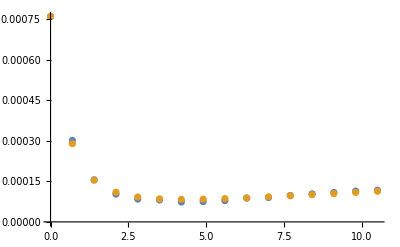

```mathematica
ListPlot[{forFit,Transpose[{steps,forFit[[1,2]]+step3[[6,2,4,1,2]][[2]]}]},PlotRange->All]
```